```mathematica
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
{(* Hamiltonian and Master equation *)
(* Basis :
State 1 = L1 ; State 2 = L2 ;
  State 3 = R1 ; State 4 = R2  *)
H=({{(ϵ-ϵ0)/2, 0, g1, -g2}, {0, ΔL+(ϵ-ϵ0)/2, -g2, g1}, {g1, -g2, -(ϵ-ϵ0)/2, 0}, {-g2, g1, 0, ΔR-(ϵ-ϵ0)/2}}); 
Hduplicate=({{(ϵ-ϵ0)/2, 0, g1, -g2}, {0, ΔL+(ϵ-ϵ0)/2, -g2, g1}, {g1, -g2, -(ϵ-ϵ0)/2, 0}, {-g2, g1, 0, ΔR-(ϵ-ϵ0)/2}}); (* all quantities is in units of angular frequency *)
densitymatrix=({{ρ11[t], ρ12[t], ρ13[t], ρ14[t]}, {Conjugate[ρ12[t]], ρ22[t], ρ23[t], ρ24[t]}, {Conjugate[ρ13[t]], Conjugate[ρ23[t]], ρ33[t], ρ34[t]}, {Conjugate[ρ14[t]], Conjugate[ρ24[t]], Conjugate[ρ34[t]], ρ44[t]}});
dephasing=({{0, γ ρ12[t], ΓL1R1 ρ13[t], ΓL1R2 ρ14[t]}, {γ Conjugate[ρ12[t]], 0, ΓL2R1 ρ23[t], ΓL2R2 ρ24[t]}, {ΓL1R1 Conjugate[ρ13[t]], ΓL2R1 Conjugate[ρ23[t]], 0, γ ρ34[t]}, {ΓL1R2 Conjugate[ρ14[t]], ΓL2R2 Conjugate[ρ24[t]], γ Conjugate[ρ34[t]], 0}});
commutator=Simplify[H.densitymatrix-densitymatrix.H];
eqn=ⅈ *D[densitymatrix,t]-commutator-dephasing//Simplify; (*master equation *)
};
{(* Parameters *)
hbar=((6.626*10^-34)/(2π));
q=1.602*10^-19;
ϵ0=ΔL/2;
ΔL=100*10^-6*(q/hbar); (* ST splitting of left dot  *)
ΔR=20*10^-6*(q/hbar); (* ST splitting of right dot  *)
g1=2.7*10^9*(2π); 
g2=3.5*10^9*(2π); 
trise=80*10^-12; (* rise time *)
tpulse1=π/(g1/2π);
(* tpulse2=4π/(g2/2π); *) (* The duration of the second pulse is a variable *)
toffset=tpulse1+trise/2;
tmeasure=5*10^-9;
ϵpulse1=ϵ0;

δ = 0;

(* ϵpulse2=-200*10^-6*(q/hbar); *) (* The height of the second pulse is a variable *)
ϵrise1=UnitStep[t](1+Sin[ (t/(trise/π)-π/2)])/2 UnitStep[-(t-trise)] * Sin[ω t + δ];
ϵrabi1=UnitStep[t-trise]UnitStep[-(t-tpulse1)] Sin[ω t + δ];
ϵfall1=UnitStep[t-tpulse1]UnitStep[-(t-tpulse1-trise)]((1+Cos[ (t-tpulse1)/(trise/π)])/2) * Sin[ω t + δ];
ϵ1=ϵpulse1*(ϵrise1+ϵrabi1+ϵfall1);
(*
de=0.6*10^-6*q/hbar; (* energy steps *)
dt=10*10^-12; (* time steps *)
*)

ωStart =  π 10/tpulse1;
ωEnd = 2 π 10/tpulse1;

dV=2;dω=(ωEnd - ωStart)/100;
nrows=2;Do[nrows+=1,{m,10,150,dV}] ; (* number of rows -- ϵpulse2 *)
ncols=2;Do[ncols+=1,{i,ωStart,ωEnd,dω}]; (* number of columns -- tpulse2 *)
γ=0;
ΓL1R1=0;
ΓL1R2=0;
ΓL2R1=0;
ΓL2R2=0;
};
Print["simdata: = ",ncols]

{(* Calculate ground state at start of pulse *)
evec=Eigenvectors[Hduplicate/.ϵ->0//N];
eval=Eigenvalues[Hduplicate/.ϵ->0//N];
grd=Min[eval];
pos=Position[eval,grd][[1]][[1]];
φ=evec[[pos]];
rho0=Outer[Times,φ,φ];
};
 
(*
Plot[{ϵrise1+ϵrabi1+ϵfall1,ϵrise2+ϵrabi2+ϵfall2,ϵrise1+ϵrabi1+ϵfall1+ϵrise2+ϵrabi2+ϵfall2},{t,0,tpulse1+tpulse2+2*trise},GridLines->{{trise/2,tpulse1,tpulse1+trise/2,tpulse1+trise,tpulse1+trise+tpulse2},None},PlotPoints->800,PlotRange->All,ImageSize->500,PlotStyle->{Red,Blue,{Black,Thick}}]
*)
tic=AbsoluteTime[];
simdata=ConstantArray[0,ncols];
col=1;
```

Remove::rmnsm: There are no symbols matching "Global`*".

simdata: = 103

```mathematica
Do[(*Vary pulse frequency *)
{
row=1;
tpulse2=1*10^-12;
tpulseend=tpulse2+trise+toffset;

ω = n *dω + ωStart;

(* Numerically solve for density matrix elements as function of time *)
diffeq={ eqn[[1]][[1]]==0,eqn[[2]][[2]]==0,eqn[[3]][[3]]==0,eqn[[4]][[4]]==0,eqn[[1]][[2]]==0,eqn[[1]][[3]]==0,eqn[[1]][[4]]==0,eqn[[2]][[3]]==0,eqn[[2]][[4]]==0,
eqn[[3]][[4]]==0,
ρ11[0]==1,ρ22[0]==0,ρ33[0]==0,ρ44[0]==0,ρ12[0]==0,ρ13[0]==0,ρ14[0]==0,ρ23[0]==0,ρ24[0]==0,ρ34[0]==0}/.ϵ->ϵ1;
sol=NDSolve[diffeq,{ρ11[t],ρ22[t],ρ33[t],ρ44[t],ρ12[t],ρ13[t],ρ14[t],ρ23[t],ρ24[t],ρ34[t]},{t,0,tpulseend+tmeasure},PrecisionGoal->7,AccuracyGoal->7,Method->{"StiffnessSwitching"},MaxSteps->Infinity]//Flatten;

prob21=1/tmeasure NIntegrate[Abs[ρ33[t]+ρ44[t]/.sol],{t,tpulseend,tpulseend+tmeasure}];
simdata[[col]]=prob21;

NotebookDelete[prw],
prw=PrintTemporary[{"n",col," : ",prob21}],

,
col=col+1;
},
{n,ωStart,ωEnd,dω}]

toc=AbsoluteTime[];
Print["Total time taken (min) = ",N[(toc-tic)/60,2]]
```

$Aborted

Total time taken (min) = 0.28

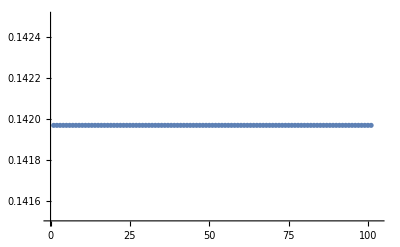

```mathematica
ListPlot[simdata, PlotRange->{0.1415,0.1425}]
```

2.69144×10^11

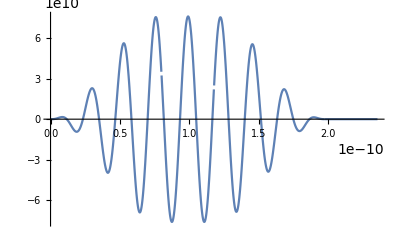

```mathematica
ω = 1*dω + ωStart
Plot[ϵ1, {t, 0, tpulse1*2} ]
```

```mathematica
sol=NDSolve[diffeq,{ρ11[t],ρ22[t],ρ33[t],ρ44[t],ρ12[t],ρ13[t],ρ14[t],ρ23[t],ρ24[t],ρ34[t]},{t,0,tpulseend+tmeasure},PrecisionGoal->7,AccuracyGoal->7,Method->{"StiffnessSwitching"},MaxSteps->Infinity]//Flatten;
```

```mathematica
v
```

v

```mathematica
dω
```

2.66479×10^9

```mathematica
TensorProduct[ {1, 1}, {2, 2}]
```

{{2,2},{2,2}}